# ERROR ANALYSIS

## Lab Report

## Names: Aryan Malhtora Lab Partner: Aili Kelley Section: H4 Date: 09/11/2024

## Purpose

To understand terminology and concepts used in measurements. 
To apply these concepts in a simple experimental situation.
To become familiar with the use of Mathematica.

## Introduction

For a scientist to arrive at a valid conclusion in testing a theory or hypothesis it is necessary to understand the underlying concepts of measurement errors. In engineering and manufacturing these same concepts are important in designing and making quality products.

In statistics, an error (or residual) is not a “mistake” but rather a difference between a computed, estimated, or measured value and the accepted true, specified, or theoretically correct value. In science and engineering in general an error is defined as a difference between the desired and actual performance or behavior of a system or object.

## Readings

Books:
P. R. Bevington, “Data Reduction and Error Analysis for the Physical Sciences”, McGrawHill. Chapter 1 and 2.3
John R. Taylor, “An Introduction to Data analysis”, University Science Books. Chapters 1 to 5.

The above chapters are available through ‘Files/Books’ folder on your Canvas.

It is recommended to read this Tutorial.
Also you have a useful formula sheet for the Principal Formulas.

### Theory and Concepts in Short

Say we measure a variable X multiple times and get the values x_1, x_2, …, x_N.
The average (arithmetic mean) of this measurement is,

μ̂= (∑_(i=1)^n x_i)/N

This formula says: Add the N measurements x_1, x_2, …, x_N. Now divide by N to get the average value of x, namely μ̂.
An estimate of the uncertainty of a single measurement, x_i, is given by the standard deviation σ defined as
σ=√((∑_(i=1)^n (x_i-μ̂)^2)/(N-1).)
If we write x_i ± σ for a single measurement, then this implies that, with a high probability, true or expected value of x_i lies between x_i+σ and x_i-σ.
If we have a theory to know that X would have a Gaussian or Normal distribution, this probability is about 68%. If needed, one can consider x_i± 2σ for about 95% probability.
An estimate of the uncertainty in the measurement of the mean μ is given by  the standard error of the mean σ̄,
σ̄= σ/(√N)=√((∑_(i=1)^n (x_i-μ̂)^2)/(N(N-1)).)= (∑_(i=1)^n μ)/N
Thus, we can write the mean as μ̂ ± σ̄, which means that there is a 68% probability that the mean value of x, namely μ, lies between μ̂+σ̄ and μ̂-σ̄.
Again, if one wants to be safer, they can consider μ̂± 2 σ̄, which means μ lies in the range μ̂- 2 σ̄ and μ̂+2 σ̄ with 95% probability.
The hat we used above means that we are estimating the mean μ with the average of a sample. We did not use hat notation for σ above, because in this lab we will not be concerned about the error with estimating the standard deviation.
Usually it is clear from the context if we are talking about the mean μ  itself or the estimation. So one might not use the hat sign at all.

Histogram of measurements distribution displays how many times a measurement lies in a given interval. The various intervals are called “bins”. The appearance and usefulness of a histogram is strongly influenced by the size of a bin. It is desirable to have a large bin size in order to make the number per bin (n) large. Then the fluctuations in “n” from bin to bin will be relatively small. On the other hand it is desirable to have the bin size small enough so as not to obscure the shape of the variation of “n”. It is an art to pick the bin size that best displays your experimental results. Note that as the number of measurements increases, the histogram becomes smoother.

A Gaussian or Normal distribution function is usually used to approximate a histogram which only contains random errors. Not all random variables would show a Gaussian curve as a histogram, but usually Gaussian distribution is a good approximation.

Example 1.
As an example of how you would use these concepts, suppose the students in a class are randomly assigned to one of three groups, each with N students. First and second group are taught some new concept using one teaching technique, while the third group is taught the same concept using a different technique. The three groups are then given the same exam on the material. We’ll call the average exam scores for the three groups μ_1, μ_2, and μ_3, and the standard errors of the means (σ̄)_1, (σ̄)_2 and (σ̄)_3. 

We would expect the difference |μ_1-μ_2|to be “small” since the two groups were taught the same way and we would like to attribute the difference to just random measuring errors. On the other hand, in order to say that the two different teaching methods produce different learning results we need to be able to say that |μ_1-μ_3| is “large”.
But small or large compared to what? The answer is small or large compared to the error in determining |μ_1-μ_2| (or |μ_1-μ_3|), which we’ll call Δ_12 (or Δ_13).
You calculate these errors from the standard deviations of the mean as follows: Δ_12 =√(OverBar[σ_1]^2+OverBar[σ_2]^2) and  Δ_13 =√(OverBar[σ_1]^2+OverBar[σ_3]^2), see propagation of errors. If groups 1 and 2 are not different then there is about 68% probability that  |μ_1-μ_2|will be less than or equal to Δ_12, or about 95% that it will be less than/equal to 2Δ_12, and a 99.7% that it will be less than/equal to 3Δ_12. The UnderBar[scientific convention] is to say two measurements are significantly (or statistically) different if they differ by three standard deviations or more. Thus we say that groups 1 and 2 are not significantly different provided |μ_1-μ_2|< 3Δ_12. Likewise, groups 1 and 3 are significantly different if |μ_1-μ_3|⩾3 Δ_13.

### Data

The Data section includes a clear and organized documentation of the observations and measurement which were made during the lab. The Data section may include a table of measurements organized in rows and columns with the column headings indicating the quantities being measured. Data sections may include diagrams of an experimental set-up with observations recorded on the diagram. The use of sentences and lengthy paragraphs is not necessary. Elaborate discussions are discouraged. But clearly labeled and documented findings are essential. These findings become the evidence which allow you to draw a conclusion related to the question described by the Purpose.

The Data section will often include calculated data. Work should be shown for each type of calculation which is performed. If the same type of calculation is repeatedly performed, the work only needs to be shown once. This work should be clear and labeled.

The Data section often includes a graph. The axes of the graph should be clearly labeled. When the graph is a representation of collected data and we are expecting a linear relation, you will often be asked to determine the slope, y-intercept, regression coefficient, and equation. The equation is often written in slope-intercept form for a linear graph. The equation should include symbols for the variables being plotted – not the traditional y and x often used in math class.

### Significant figures

Be sure to read section on significant figures and quote all results accordingly. In general, the uncertainty is quoted to only one significant figure unless that is a 1, in which case it is sometimes quoted to two (i.e., 0.3, not 0.33, but 0.1 or 0.13 would be acceptable). The value should be quoted to the same precision as the error, or at most one more. For example, give 2.5 ± 0.4 not 2.543 ± 0.4 and not 2.5 ± 0.007, although 2.54 ± 0.1 or 2.54 ± 0.14 would be acceptable.

### Some References to Mathematica Commands

In this course we will try to provide examples on how to do any computational task using Mathematica. You will only need to tweak the code and make it match your choice of file names or variable names or .... Remember that the equal sign in programming is usually used for assignment.
You can also use the documentation whenever you need. For example, this is a list of Mathematica commands we will use in this lab,
ReadList, Histogram, TableForm, Plot, Join, Mean, StandardDeviation

## Procedure

In this experiment both you and your partner shall take two sets of data on the reaction time and compare the two sets to investigate if there is a significant difference between them. You and your partner shall calculate the average reaction time and the standard deviation for each set, make the histogram of the data distribution and overlap with normal (or Gauss) distribution. Then you shall compare one set of your data with that of your partner. You shall answer the questions below in Questions sections. 

	1. Make two sets of 40 reaction time measurements. To measure your reaction time, you will use the program stopwatch.exe. Select “Reaction Time”, and click the mouse or hit the return key once you see the little guy sticking his tongue out at you, saying “Hit Me!”. Repeat this 40 times for each set. Copy-paste the data into notepad and save in files “YourName_RT_1” and “YourName_RT_2”
	2. You shall import these data into Mathematica using command ReadList[“Insert/filepath/filename”] from a file or {InputString[]} from a dialog box, as shown in the example below.
	3. Calculate your average reaction times, OverBar[t_1], OverBar[t_2], and the standard deviations, σ_1, σ_2. Present the data in a table as it is shown in the example below. 
	4. Calculate the standard deviation of the mean. 
	5. Compare your reaction times for the two runs. 
	6. Present OverBar[t_i] with corresponding errors. Note that only the significant figures should be presented. 
	7. The lab partner should repeat all the above to obtain another two sets of 40 measurements. Calculate OverBar[t_3], OverBar[t_4], and the standard deviations, σ_3, σ_4 of the new data for the partner.
	8. Compare reaction times for you and your partner.
	9. Combine the two sets of data 1 and 2 to give a data set of 80 measurements. Make a histogram of the data and overlap with normal distribution as shown in example below. 
	10. Answer the questions below.

## Dialog:

### Step 1.

Import the data created by stopwatch into Mathematica List variable ti (i = 1, ... 4) using the command ReadList[“Insert/filepath/filename”] from a file or {InputString[]} from a dialog box.
To run a code cell, press Shift+Enter, i.e. hold down the Shift key and press the Return key (aka Enter key).
Also copy the code cells in new cells. If you copy a code or input cell inside a text cell it will not compute.

```mathematica
t1=ReadList["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Aryan_RT_1.txt"] 
t2=ReadList["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Aryan_RT_2.txt"]
```

{0.33,0.3,0.3,0.3,0.31,0.3,0.28,0.31,0.3,0.32,0.3,0.4,0.26,0.4,0.38,0.29,0.34,0.3,0.37,0.4,0.34,0.3,0.3,0.33,0.28,0.31,0.31,0.27,0.4,0.27,0.32,0.31,0.35,0.39,0.38,0.39,0.28,0.25,0.31,0.28}

{0.38,0.3,0.47,0.39,0.31,0.52,0.42,0.33,0.3,0.33,0.38,0.36,0.36,0.31,0.33,0.42,0.41,0.52,0.36,0.31,0.31,0.33,0.3,0.33,0.36,0.33,0.38,0.36,0.42,0.36,0.33,0.34,0.33,0.33,0.36,0.28,0.3,0.36,0.33,0.34}

or {InputString[]} from a dialog box

```mathematica
(*t1={InputString[]} *)
```

### Step 2.

Calculate the number of measurements “n1”, and their average “μ_1”.

```mathematica
n1=Length[t1]
mu1= (∑_(i=1)^n1 t1[[i]])/n1
```

40

0.3215

### Step 3.

Calculate the deviation from average dev1=(t_1-μ_1) and its square  dev1p2=(t_1-μ_1)^2 and present results in a table.

```mathematica
dev1=t1-mu1;
dev1p2=dev1^2;
TableForm[{{t1,dev1, dev1p2}}, TableAlignments->Center, TableHeadings->{None,{"t1_i","t1_i-μ_1", "(t1_i-μ_1)^2"}}]
```

t1_i | t1_i-μ_1 | (t1_i-μ_1)^2
0.33
0.3
0.3
0.3
0.31
0.3
0.28
0.31
0.3
0.32
0.3
0.4
0.26
0.4
0.38
0.29
0.34
0.3
0.37
0.4
0.34
0.3
0.3
0.33
0.28
0.31
0.31
0.27
0.4
0.27
0.32
0.31
0.35
0.39
0.38
0.39
0.28
0.25
0.31
0.28 | 0.0085
-0.0215
-0.0215
-0.0215
-0.0115
-0.0215
-0.0415
-0.0115
-0.0215
-0.0015
-0.0215
0.0785
-0.0615
0.0785
0.0585
-0.0315
0.0185
-0.0215
0.0485
0.0785
0.0185
-0.0215
-0.0215
0.0085
-0.0415
-0.0115
-0.0115
-0.0515
0.0785
-0.0515
-0.0015
-0.0115
0.0285
0.0685
0.0585
0.0685
-0.0415
-0.0715
-0.0115
-0.0415 | 0.00007225
0.00046225
0.00046225
0.00046225
0.00013225
0.00046225
0.00172225
0.00013225
0.00046225
2.25×10^-6
0.00046225
0.00616225
0.00378225
0.00616225
0.00342225
0.00099225
0.00034225
0.00046225
0.00235225
0.00616225
0.00034225
0.00046225
0.00046225
0.00007225
0.00172225
0.00013225
0.00013225
0.00265225
0.00616225
0.00265225
2.25×10^-6
0.00013225
0.00081225
0.00469225
0.00342225
0.00469225
0.00172225
0.00511225
0.00013225
0.00172225

### Step 4.

Calculate standard deviation, “sigma1”, and standard deviation of the mean, “sigma1bar”.

```mathematica
sigma1=√((∑_(i=1)^n1 dev1p2[[i]])/(n1-1))
sigma1bar=√((∑_(i=1)^n1 dev1p2[[i]])/(n1*(n1-1)))
```

0.04294

0.00678941

#### Question 1:

Use the data to calculate:
(a) How far your car travels at 50 mph before you hit the brakes after you see a traffic light change. (1 mi = 5,280 ft = 1610 m). This is the mean “reaction distance”; that is the distance it takes you to react. Your brakes can stop your car in 180 feet once you apply the brakes. 
(b) What is the maximum and minimum distances (at a 95% confidence level) that you will travel before stopping after the light changes. Show your reasoning and analysis . 
(c) Based on this, how much distance should you leave between you and the car in front of you when traveling at 50 mph.
 
Show all calculation below. Do this question for only one set of data but specify which data set you are using.

#### Answer 1:

a) We know my mean reaction time is mu1. That means, before hitting the brakes, my car would, ON AVERAGE, continue to go at the speed of 50mph for time mu1.

```mathematica
meanReactionDistance=mu1*(50*1610/3600) (*in meters*)
```

7.1891

b) Considering the Reaction times to have a Gaussian Distribution, we can say, with about 95% confidence that any 1 particular value for the reaction time would be within range mu1-2sigma1 to mu1+2sigma2. The reaction distances with 95% probabilities would thus be those times the speed. Thus total distance would be reaction distance + 180 feet (as mentioned in the question, we take 180 feet to stop after hitting the breaks)

```mathematica
min_dist_95=(mu1-2sigma1)* (50*1610/3600) + 180*(1610/5280) (*in meters*)
```

Set::write: Tag Times in 95 _ min_dist is Protected.

60.1551

```mathematica
max_dist_95=(mu1+2sigma1)* (50*1610/3600) + 180*(1610/5280) (*in meters*)
```

Set::write: Tag Times in 95 _ max_dist is Protected.

63.9958

```mathematica
break_distance = N[180*(1610/5280), 5] (*in meters*)
```

54.886

My reaction distance with 95% confidence is about 10m. Say the car in front of me sees the traffic light turn red, it applies breaks. 
I would have travelled 10m before seeing those lights turn red (given that he instantaneously saw the lights turn red). Even if not the lights, with 95% confidence, I would have seen him break and would only have moved 10m before I hit the breaks myself.

Thereafter, both the cars would be in the “Breaking” stage where they would travel their 55m of break distance. That is to say, seeing the driver hit breaks, I would indeed take 55m to stop my car. But by no means would the car in front of me stop instantaneously, it would also have to travel 55m, allowing me to leave lesser space than what one would anticipate.

So there is no need to leave 65m of distance. A more practically viable distance to leave, even at that speed would be something close to the reaction distance for the speed. I.e. around 10m.

(for safety, let’s assume we leave 15-20m of space. This would thus be way lower than the naive 65m distance)

Thus, based on the data, it is decently safe to maintain a 15m (m=meters) distance from the car in front of me, even when going at 50mph (m=miles)

### Step 5.

Repeat steps 1-4 for your second set of measurements “t2”. Calculate their average “mu2”, deviation from average “dev2”, and square of the deviation “dev2p2”,  standard deviation, “sigma2”, and standard deviation of the mean, “sigma2bar”. You can copy the code and only tweak if needed. And no need to answer the Question 1 again.

```mathematica
(*Step 1 for set 2*)
```

```mathematica
n2=Length[t2]
mu2= (∑_(i=1)^n1 t2[[i]])/n2
```

40

0.35725

```mathematica
(*Step 2 for set 2*)
dev2=t2-mu2;
dev2p2=dev2^2;
TableForm[{{t2,dev2, dev2p2}}, TableAlignments->Center, TableHeadings->{None,{"t2_i","t2_i-μ_2", "(t2_i-μ_2)^2"}}]

(*Step 3 for set 2*)
sigma2=√((∑_(i=1)^n1 dev2p2[[i]])/(n2-1))
sigma2bar=√((∑_(i=1)^n1 dev2p2[[i]])/(n2*(n2-1)))
```

t2_i | t2_i-μ_2 | (t2_i-μ_2)^2
0.38
0.3
0.47
0.39
0.31
0.52
0.42
0.33
0.3
0.33
0.38
0.36
0.36
0.31
0.33
0.42
0.41
0.52
0.36
0.31
0.31
0.33
0.3
0.33
0.36
0.33
0.38
0.36
0.42
0.36
0.33
0.34
0.33
0.33
0.36
0.28
0.3
0.36
0.33
0.34 | 0.02275
-0.05725
0.11275
0.03275
-0.04725
0.16275
0.06275
-0.02725
-0.05725
-0.02725
0.02275
0.00275
0.00275
-0.04725
-0.02725
0.06275
0.05275
0.16275
0.00275
-0.04725
-0.04725
-0.02725
-0.05725
-0.02725
0.00275
-0.02725
0.02275
0.00275
0.06275
0.00275
-0.02725
-0.01725
-0.02725
-0.02725
0.00275
-0.07725
-0.05725
0.00275
-0.02725
-0.01725 | 0.000517563
0.00327756
0.0127126
0.00107256
0.00223256
0.0264876
0.00393756
0.000742562
0.00327756
0.000742562
0.000517563
7.5625×10^-6
7.5625×10^-6
0.00223256
0.000742562
0.00393756
0.00278256
0.0264876
7.5625×10^-6
0.00223256
0.00223256
0.000742562
0.00327756
0.000742562
7.5625×10^-6
0.000742562
0.000517563
7.5625×10^-6
0.00393756
7.5625×10^-6
0.000742562
0.000297562
0.000742562
0.000742562
7.5625×10^-6
0.00596756
0.00327756
7.5625×10^-6
0.000742562
0.000297562

0.0552378

0.00873387

### Step 6.

Now create a table of six columns (t1,dev1,dev1p2,t2,dev2,dev2p2) for both sets of your measurements:

```mathematica
TableForm[{{t1,dev1, dev1p2,t2,dev2, dev2p2}}, TableAlignments->Center, TableHeadings->{None,{"t1_i","t1_i-μ_1", "(t1_i-μ_1)^2","t2_i","t2_i-μ_2", "(t2_i-μ_2)^2"}}]
TableForm[{{Sum[t1[[i]],{i,n1}],Sum[dev1[[i]],{i,n1}], Sum[dev1p2[[i]],{i,n1}],Sum[t2[[i]],{i,n2}],Sum[dev2[[i]],{i,n2}], Sum[dev2p2[[i]],{i,n2}]}}, TableAlignments->Center, TableHeadings->{None,{"∑_(i=1)^n1 t1_i","∑_(i=1)^n1 (t1_i-μ_1)", "∑_(i=1)^n1 (t1_i-μ_1)^2","∑_(i=1)^n2 t2_i","∑_(i=1)^n2 (t2_i-μ_2)", "∑_(i=1)^n2 (t2_i-μ_2)^2"}}]
```

t1_i | t1_i-μ_1 | (t1_i-μ_1)^2 | t2_i | t2_i-μ_2 | (t2_i-μ_2)^2
0.33
0.3
0.3
0.3
0.31
0.3
0.28
0.31
0.3
0.32
0.3
0.4
0.26
0.4
0.38
0.29
0.34
0.3
0.37
0.4
0.34
0.3
0.3
0.33
0.28
0.31
0.31
0.27
0.4
0.27
0.32
0.31
0.35
0.39
0.38
0.39
0.28
0.25
0.31
0.28 | 0.0085
-0.0215
-0.0215
-0.0215
-0.0115
-0.0215
-0.0415
-0.0115
-0.0215
-0.0015
-0.0215
0.0785
-0.0615
0.0785
0.0585
-0.0315
0.0185
-0.0215
0.0485
0.0785
0.0185
-0.0215
-0.0215
0.0085
-0.0415
-0.0115
-0.0115
-0.0515
0.0785
-0.0515
-0.0015
-0.0115
0.0285
0.0685
0.0585
0.0685
-0.0415
-0.0715
-0.0115
-0.0415 | 0.00007225
0.00046225
0.00046225
0.00046225
0.00013225
0.00046225
0.00172225
0.00013225
0.00046225
2.25×10^-6
0.00046225
0.00616225
0.00378225
0.00616225
0.00342225
0.00099225
0.00034225
0.00046225
0.00235225
0.00616225
0.00034225
0.00046225
0.00046225
0.00007225
0.00172225
0.00013225
0.00013225
0.00265225
0.00616225
0.00265225
2.25×10^-6
0.00013225
0.00081225
0.00469225
0.00342225
0.00469225
0.00172225
0.00511225
0.00013225
0.00172225 | 0.38
0.3
0.47
0.39
0.31
0.52
0.42
0.33
0.3
0.33
0.38
0.36
0.36
0.31
0.33
0.42
0.41
0.52
0.36
0.31
0.31
0.33
0.3
0.33
0.36
0.33
0.38
0.36
0.42
0.36
0.33
0.34
0.33
0.33
0.36
0.28
0.3
0.36
0.33
0.34 | 0.02275
-0.05725
0.11275
0.03275
-0.04725
0.16275
0.06275
-0.02725
-0.05725
-0.02725
0.02275
0.00275
0.00275
-0.04725
-0.02725
0.06275
0.05275
0.16275
0.00275
-0.04725
-0.04725
-0.02725
-0.05725
-0.02725
0.00275
-0.02725
0.02275
0.00275
0.06275
0.00275
-0.02725
-0.01725
-0.02725
-0.02725
0.00275
-0.07725
-0.05725
0.00275
-0.02725
-0.01725 | 0.000517563
0.00327756
0.0127126
0.00107256
0.00223256
0.0264876
0.00393756
0.000742562
0.00327756
0.000742562
0.000517563
7.5625×10^-6
7.5625×10^-6
0.00223256
0.000742562
0.00393756
0.00278256
0.0264876
7.5625×10^-6
0.00223256
0.00223256
0.000742562
0.00327756
0.000742562
7.5625×10^-6
0.000742562
0.000517563
7.5625×10^-6
0.00393756
7.5625×10^-6
0.000742562
0.000297562
0.000742562
0.000742562
7.5625×10^-6
0.00596756
0.00327756
7.5625×10^-6
0.000742562
0.000297562

∑_(i=1)^n1 t1_i | ∑_(i=1)^n1 (t1_i-μ_1) | ∑_(i=1)^n1 (t1_i-μ_1)^2 | ∑_(i=1)^n2 t2_i | ∑_(i=1)^n2 (t2_i-μ_2) | ∑_(i=1)^n2 (t2_i-μ_2)^2
12.86 | -2.33147×10^-15 | 0.07191 | 14.29 | 1.77636×10^-15 | 0.118998

### Step 7.

Create a table of mean times and standard deviations for your two set of measurements:

```mathematica
TableForm[{{mu1,sigma1, sigma1bar,mu2,sigma2, sigma2bar}}, TableAlignments->Center, TableHeadings->{None,{"μ_1","σ_1", "OverBar[σ_1]","μ_2","σ_2", "OverBar[σ_2]"}}]
```

μ_1 | σ_1 | OverBar[σ_1] | μ_2 | σ_2 | OverBar[σ_2]
0.3215 | 0.04294 | 0.00678941 | 0.35725 | 0.0552378 | 0.00873387

Write results below to the correct number of significant digits :

μ_1±OverBar[σ_1]=0.32±0.007 ≈0.33
μ_2±OverBar[σ_2]= 0.36±0.009 ≈ 0.37

μ= (∑_(i=1)^n t[[i]])/n since all our measurements have both significant figures and decimal places = 2. 
Summing up each of the 2 decimal places numbers, we should have a final result that is 2 decimal places. When we divide it through, the number of significant figures (2) remain the same.
Hence both μ’s must have significant figures.

Hence, considering the significant figures, μ_1=0.32, μ_2=0.36

sigma=√((∑_(i=1)^n devp2[[i]])/(n(n-1)))  devp2 is (deviation)*(deviation)=(ti-mu)*(ti-mu)
since ti has 2 significant figures/digits after decimals, deviations must also have 2 decimals places (number of decimal places remain the same during addition)

(thus each dev must have form 0.0x in my data)
Thus devp2 must have the same significant figures as deviations (i.e. 1)

The lowest number of digits after decimals in my data would thus be 3 digits.(0.00x) and hence 1 significant figure.
dividing through by n(n-1) would make no difference since it has infinite precision so significant figures remain the same. Square rooting a number would also maintain the same significant digits (a*a has same sig-figs as a. By induction, a^(1/2) must have same sigfigs as a).

Hence, sigma’s must be 1 significant digit.

Since all sigma’s are more than 2 digits for each of them being 1 sig-figure, each term must have 2 decimal places.

Compare your reaction times for the two runs.  [Here you can find a example for meaningful comparison of two sets of data.]

|μ_1-μ_2|=0.03575

 Δ_12 =√(OverBar[σ_1]^2+OverBar[σ_2]^2)=0.0110624

R_12=(|μ_1-μ_2|)/(√(OverBar[σ_1]^2+OverBar[σ_2]^2))=3.23167

```mathematica
diff=Abs[mu1-mu2]
sig = (sigma1bar^2+sigma2bar^2)^(1/2)
diff/sig
```

0.03575

0.0110624

3.23167

“If groups 1 and 2 are not different then there is about 68% probability that  |μ_1-μ_2|will be less than or equal to Δ_12, or about 95% that it will be less than/equal to 2Δ_12, and a 99.7% that it will be less than/equal to 3Δ_12. The UnderBar[scientific convention] is to say two measurements are significantly (or statistically) different if they differ by three standard deviations or more. Thus we say that groups 1 and 2 are not significantly different provided |μ_1-μ_2|< 3Δ_12. Likewise, groups 1 and 3 are significantly different if |μ_1-μ_3|⩾3 Δ_13.” - Theoretical Reasoning Provided in the Above passage.

Since my |μ_1-μ_2| is actually > 3Δ_12, it can be scientifically said that the two sets of reaction-times were different.
They were my own reaction times. I would argue that it shows I was significantly more attentive to the task of clicking the stopwatch the the starting. My focus dropped off as time passed by, hence I performed significantly worse in the 2nd set, hence the two sets were evidently different.

### Step 8.

Combine the two sets of data for t1 and t2 to give a data set of 80 measurements

```mathematica
t12=Join[t1,t2]
```

{0.33,0.3,0.3,0.3,0.31,0.3,0.28,0.31,0.3,0.32,0.3,0.4,0.26,0.4,0.38,0.29,0.34,0.3,0.37,0.4,0.34,0.3,0.3,0.33,0.28,0.31,0.31,0.27,0.4,0.27,0.32,0.31,0.35,0.39,0.38,0.39,0.28,0.25,0.31,0.28,0.38,0.3,0.47,0.39,0.31,0.52,0.42,0.33,0.3,0.33,0.38,0.36,0.36,0.31,0.33,0.42,0.41,0.52,0.36,0.31,0.31,0.33,0.3,0.33,0.36,0.33,0.38,0.36,0.42,0.36,0.33,0.34,0.33,0.33,0.36,0.28,0.3,0.36,0.33,0.34}

Using the function Histogram[t12,nbar] make a histogram of data. nbar specifies the number of bins. Experiment with different values of nbar to produce a meaningful histogram for this data.

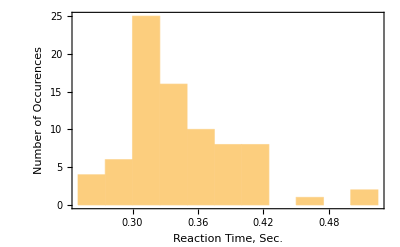

```mathematica
Histogram[t12,{0.025}, Frame->True, FrameLabel->{"Reaction Time, Sec." ,"Number of Occurences"}]
```

#### Question 2:

Using Drawing Tools [CTRL-d] indicate μ value and the ranges μ±σ, μ±2σ, etc., on the histogram. Determine the percent of the measurements falling within these ranges.

#### Answer 2:

```mathematica
avgmu=(mu1+mu2)/2
sigma _my= ((sigma1^2+sigma2^2)/2)^(1/2)
dev=t12-avgmu;
devp2=dev^2;
sigma=√((∑_(i=1)^n1 devp2[[i]])/(Length[t12]-1))
avgmu+sigma 
avgmu -sigma 
avgmu + 2*sigma 
avgmu - 2*sigma

Histogram[t12,{0.025}, Frame->True, FrameLabel->{"Reaction Time, Sec." ,"Number of Occurences"}]
```

0.339375

Set::write: Tag Times in 0.0327419 _my is Protected.

0.0494725

0.0327419

0.372117

0.306633

0.404859

0.273891

-Graphics-

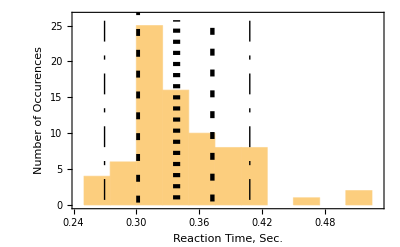

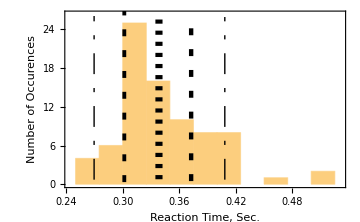

The finely-dotted line here is the mean value. The dashed line is the μ±σ sigma line where sigma has been recalculated for set t12. The Dash-Dot line is the μ±2σ mark. Although it might feel that the marks do not actually include the 95% measurements of the experiment, they might not have to. Since the graph of my measurements is not a perfect gaussian, it is bound to have errors in the statistical analysis. But it gives fairly accurate insights about the reaction times and distances.

### Step 9.

As the number of measurements increases, the histogram becomes smoother.
As we said, a good approximation which is conventional to use for the histogram is the Gaussian distribution function. The Gaussian function is given by:
P_G[x]=1/(√(2*π)*σ)*ⅇ^((-(x-μ)^2)/(2*(σ)^2)).
Plot the normal distribution for data t12:

80

0.0523461

0.339375

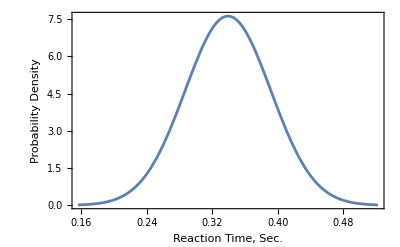

```mathematica
n12=Length[t12]
σ12=StandardDeviation[t12]
μ12=Mean[t12]
P[x_,  μ_, σ_]:=1/(√(2*π)*σ)*ⅇ^((-(x-μ)^2)/(2*(σ)^2));
Plot[P[x1, μ12, σ12],{x1,μ12-3.5 σ12,μ12+3.5 σ12},PlotRange->All, Frame->True, FrameLabel->{"Reaction Time, Sec." ,"Probability Density"}]
```

### Step 10.

Using the command the Mathematica function Show plot the histogram and normal distribution of the data together.
Notice that the argument “ProbabilityDensity” in Histogram[t12,nbar,“ProbabilityDensity”]  plots the normalized histogram for t12.

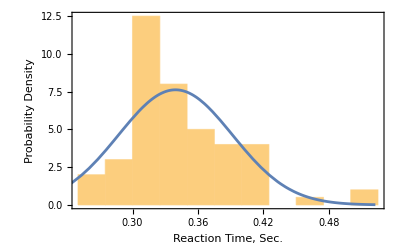

```mathematica
Show[Histogram[t12,{.025},"PDF"],Plot[P[x1, Mean[t12],StandardDeviation[t12]],{x1,Mean[t12]-3.5 StandardDeviation[t12],Mean[t12]+3.5 StandardDeviation[t12]},PlotRange->Automatic], Frame->True, FrameLabel->{"Reaction Time, Sec." ,"Probability Density"}]
```

### Step 11.

Repeat steps 1-4 for set of measurements “t3” of your lab partner. Calculate their average “mu3”, standard deviation, “sigma3”, and standard deviation of the mean, “sigma3bar”.

```mathematica
t3={0.58,0.38,0.3,0.38,0.39,0.5,0.31,0.33,0.33,0.52,0.36,0.38,0.38,0.36,0.41,0.33,0.39,0.36,0.36,0.39,0.58,0.91,0.69,0.39,0.48,0.38,0.36,0.41,0.47,0.44,0.66,0.38,0.38,0.47,0.41,0.39,0.39,0.42,0.36,0.39}
```

{0.58,0.38,0.3,0.38,0.39,0.5,0.31,0.33,0.33,0.52,0.36,0.38,0.38,0.36,0.41,0.33,0.39,0.36,0.36,0.39,0.58,0.91,0.69,0.39,0.48,0.38,0.36,0.41,0.47,0.44,0.66,0.38,0.38,0.47,0.41,0.39,0.39,0.42,0.36,0.39}

```mathematica
n3=Length[t3]
```

40

```mathematica
mu3= (∑_(i=1)^n3 t3[[i]])/n3
```

0.4275

```mathematica
(*Step 2 for set 3*)
dev3=t3-mu3;
dev3p2=dev3^2;
TableForm[{{t3,dev3, dev3p2}}, TableAlignments->Center, TableHeadings->{None,{"t3_i","t3_i-μ_3", "(t3_i-μ_3)^2"}}]

(*Step 3 for set 3*)
sigma3=√((∑_(i=1)^n3 dev3p2[[i]])/(n3-1))
sigma3bar=√((∑_(i=1)^n3 dev3p2[[i]])/(n3*(n3-1)))
```

t3_i | t3_i-μ_3 | (t3_i-μ_3)^2
0.58
0.38
0.3
0.38
0.39
0.5
0.31
0.33
0.33
0.52
0.36
0.38
0.38
0.36
0.41
0.33
0.39
0.36
0.36
0.39
0.58
0.91
0.69
0.39
0.48
0.38
0.36
0.41
0.47
0.44
0.66
0.38
0.38
0.47
0.41
0.39
0.39
0.42
0.36
0.39 | 0.1525
-0.0475
-0.1275
-0.0475
-0.0375
0.0725
-0.1175
-0.0975
-0.0975
0.0925
-0.0675
-0.0475
-0.0475
-0.0675
-0.0175
-0.0975
-0.0375
-0.0675
-0.0675
-0.0375
0.1525
0.4825
0.2625
-0.0375
0.0525
-0.0475
-0.0675
-0.0175
0.0425
0.0125
0.2325
-0.0475
-0.0475
0.0425
-0.0175
-0.0375
-0.0375
-0.0075
-0.0675
-0.0375 | 0.0232562
0.00225625
0.0162563
0.00225625
0.00140625
0.00525625
0.0138063
0.00950625
0.00950625
0.00855625
0.00455625
0.00225625
0.00225625
0.00455625
0.00030625
0.00950625
0.00140625
0.00455625
0.00455625
0.00140625
0.0232562
0.232806
0.0689062
0.00140625
0.00275625
0.00225625
0.00455625
0.00030625
0.00180625
0.00015625
0.0540562
0.00225625
0.00225625
0.00180625
0.00030625
0.00140625
0.00140625
0.00005625
0.00455625
0.00140625

0.11714

0.0185215

Write your results below and compare the reaction times for you and your partner:

μ_3=0.4275

σ_3=0.11714

OverBar[σ_3]=0.0185215

R_13=(|μ_1-μ_3|)/(√(OverBar[σ_1]^2+OverBar[σ_3]^2))= 5.37344

```mathematica
Subscript[R, 13] = Abs[mu1-mu3]/Sqrt[sigma1bar^2 + sigma3bar^2]
```

5.37344

#### Question 3:

Write a short paragraph on the conclusions you can draw from R_12 and R_13 .  [Here you can find a example for meaningful comparison of two sets of data.]

R12 = 3.23 and R13 = 5.38
As described earlier, since R12 > 3, that means my 2 reaction time sets were scientifically different.
Since R13 is even larger, the 2 sets are evidently more different. Specifically, the difference in their means is much larger than what their combined variation in the mean should be (sigmabar).

Hence, it is quite evident that they are sets of reaction times from 2 different people with different reaction times and focus spans, not just errors in 1 person’s reaction times/measurement errors.

#### Answer 3.

#### Question 4:

Compare the variability of the individual reaction time measurements for you and your partner. Who has the “steadier nerves” (i.e., smallest deviation)?

#### Answer 4.

In answer 3, it has been established that both our reaction sets are different.
Comparing the statistical metrics:
mu1=0.32
mu3=0.42
sigma1=0.043
sigma3=0.12

Thus, on average, I have a faster reaction time than my partner. Also, my data has a lot less variation. Meaning that my reaction times are clumped closer together. Hence I have a much more reliable information about my reaction time. That is to say, I have steadier nerves.